# Vaje za 2. teden

27. 2. 2025

## Ponovitev

Izračunaj 1+x+x^2+x^3, kjer je x = 1/√e+1/√π, na dva načina: naprej s pomočjo prepisovalnega pravila, nato pa še tako, da definiraš vrednost spremenljivke x.
Spremenljivko x na koncu pobriši.

```mathematica
1+x+x^2+x^3
```

1+x+x^2+x^3

```mathematica
%/.{x->1/√e+1/√π}
```

1+1/(√e)+(1/(√e)+1/(√π))^2+(1/(√e)+1/(√π))^3+1/(√π)

```mathematica
Clear[x]
```

```mathematica
x = 1/√e+1/√π
1+x+x^2+x^3
```

1/(√e)+1/(√π)

1+1/(√e)+(1/(√e)+1/(√π))^2+(1/(√e)+1/(√π))^3+1/(√π)

```mathematica
Clear[x]
```

## Naloga 1

Izračunaj 1000-i decimalki števil e in π na dva načina:
1. Tako da izračunaš dovolj decimalk obeh števil in pogledaš ustrezno decimalko pri koncu. Zakaj zadnja decimalka ne bo v redu? Uporabi funkcijo N tako, da ji podaš natančnost.
2. Z uporabo funkcije RealDigits in izpisom ustreznega elementa seznama.

Določi še 5., 100. in 443. decimalko.

Napiši fuknkcijo, ki sprejme poljubno realno število x in naravno število n in vrne n-to decimalko števila x.

```mathematica
N[ⅇ,1002]
```

2.7182818284590452353602874713526624977572470936999595749669676277240766303535475945713821785251664274274663919320030599218174135966290435729003342952605956307381323286279434907632338298807531952510190115738341879307021540891499348841675092447614606680822648001684774118537423454424371075390777449920695517027618386062613313845830007520449338265602976067371132007093287091274437470472306969772093101416928368190255151086574637721112523897844250569536967707854499699679468644549059879316368892300987931277361782154249992295763514822082698951936680331825288693984964651058209392398294887933203625094431173012381970684161403970198376793206832823764648042953118023287825098194558153017567173613320698112509961818815930416903515988885193458072738667385894228792284998920868058257492796104841984443634632449684875602336248270419786232090021609902353043699418491463140934317381436405462531520961836908887070167683964243781405927145635490613031072085103837505101157477041718986106873969655212671546889570350354

```mathematica
N[π,1002]
```

3.14159265358979323846264338327950288419716939937510582097494459230781640628620899862803482534211706798214808651328230664709384460955058223172535940812848111745028410270193852110555964462294895493038196442881097566593344612847564823378678316527120190914564856692346034861045432664821339360726024914127372458700660631558817488152092096282925409171536436789259036001133053054882046652138414695194151160943305727036575959195309218611738193261179310511854807446237996274956735188575272489122793818301194912983367336244065664308602139494639522473719070217986094370277053921717629317675238467481846766940513200056812714526356082778577134275778960917363717872146844090122495343014654958537105079227968925892354201995611212902196086403441815981362977477130996051870721134999999837297804995105973173281609631859502445945534690830264252230825334468503526193118817101000313783875288658753320838142061717766914730359825349042875546873115956286388235378759375195778185778053217122680661300192787661119590921642019894

```mathematica
f[x_.08,n_]:=Last[RealDigits[x,10,n+Ceiling[Log[10,x]]][[1]]];
```

## Naloga 2

V Matematico vnesi izraz sin(π/8)+cos(π/8). Kaj Mathematica vrne? Nato poskusi ta izraz poenostaviti s primernim izrazom (končni rezultat se “lepo” izrazi s koreni).Definiraj niz niz, ki bo lepo predstavil in zapisal rešitev te naloge. Po klicu spremenljivke niz naj tako Mathematica izpiše spodnji niz, kjer naj bo niz “___” nadomeščen s pravim rezultatom.
"Vsota sin(π/8) + cos(π/8) je enaka ___."

```mathematica
Sin[π/8]+Cos[π/8]
```

Cos[π/8]+Sin[π/8]

```mathematica
izraz=Sin[π/8]+Cos[π/8]//FullSimplify
izpisi=StringForm["Vsota sin(π/8) + cos(π/8) je enaka ``", izraz]
```

√(1+1/(√2))

Vsota sin(π/8) + cos(π/8) je enaka √(1+1/(√2))

## Naloga 3

Napiši  funkcijo poenostaviInIzpisi, ki  bo  sprejela  izraz “izr”, ga  poenostavila  in  rezultat  izpisala  v  obliki
“Izraz [izr] se poenostavi v izraz [poenostavljen_izraz]”,
kjer je [izr] nadomestite z vnešenim izrazom, [poenostavljen_izraz] pa s poenostavljenim izrazom.

```mathematica
poenostvilnIzpisi[izr_]:=StringForm["Izraz `` se poenostavi v izraz ``", izr,izr //FullSimplify]
```

## Naloga 4

Matej ima 249 jabolk, Jana pa 419 jabolk. Koliko jabolk imata skupaj?
Rešitev zgornje naloge predstavi z nizom, ki ga shrani v spremenljivki niz. Ob klicu spremenljivke niz naj Mathematica vrne:
“Če ima Matej 249 jabolk in Jana 419 jabolk, potem imata skupaj 249 + 419 = 668 jabolk.”
Pomagaj si z vodičem za generiranje nizov (predvsem del za vstavljanje izrazov) in uporabi funkcijo TemplateApply, da definiraš zgornji niz še brez direktnega vnašanja števila 668.

```mathematica
niz[mat_,jan_]:=TemplateApply[
StringTemplate["Če ima Matej `matej` jabolk in Jana `jana` jabolk, potem imata skupaj `matej` + `jana` = `skupaj` jabolk."],
<|"matej" ->mat,"jana"->jan,"skupaj"->mat+jan|>
]
```

```mathematica
niz[1, 2]
```

Če ima Matej 1 jabolk in Jana 2 jabolk, potem imata skupaj 1 + 2 = 3 jabolk.

## Naloga 5

1. Definiraj funkcijo f(x)=x^2+3x+2+sin(x).
2. Izračunaj f(3)+f(4).  Uporabi tako prefiksni kot postfiksni način klica funkcije. Rezultat izpiši numerično (kot približek).
3. Nariši graf funkcije f na intervalu [-10,10].
4. Definiraj funkcijo g z istim predpisom kot f, pri čemer g definiraj kot anonimno funkcijo s formalnim parametrom #.
5. Definiraj funkcijo h(x,y)=(f(x)+g(y))^2 na dva načina: na standardni način in kot anonimno funkcijo.

```mathematica
f[x_]:=x^2+3x+2+Sin[x]
```

```mathematica
f[3]+f[4]
```

50+Sin[3]+Sin[4]

## Naloga 6

1. Definiraj funkciji f(x) in g(n), kjer je f(x)=x^3+x+1, g(n) pa je ostanek števila n pri deljenju s 7.
2. Ustvari seznam {f(1),f(2),...,f(100)}. Poišči vsa števila n s tega seznama, za katere je g(n)=3. Uporabi ukaz Select.
3. Poskusi rešiti zgornjo nalogo v eni vrstici s pomočjo uporabe anonimnih funkcij.

## Naloga 7

Kaj vrne spodnja koda? Pojasni vsako vrstico!

```mathematica
VsotaKvadratov[x_,y_]:=x^2+y^2
AplicirajFunkcijo2Spremenljivk[f_,x_,y_]:=f[x,y]
AplicirajFunkcijo2Spremenljivk[VsotaKvadratov,3,4]
```

Zgornja koda vsebuje 3 vrstice. Zapiši ekvivalent te kode z uporabo anonimne funkcije, ki vsebuje le 1 vrstico.

## Naloga 8

Nariši graf funkcije f (x, y, z) = x  sin (xy)  cos (xy + z), kjer za z-koordinato uporabi  slider.

## Naloga 9

V pomoči si poglej ukaz Join. Definiraj seznam {1,2,...,100,1,2,...,100}. Definiraj še funkcijo DvojniSeznam[n], ki vrne dvojni seznam {1,2,...,n,1,2,...,n}.

Kaj dela spodnja funkcija?

```mathematica
Krogi[n_]:=Join[{Red},Table[Disk[{2i,0}],{i,n}]]
```

Definiraj funkcijo NarisiKroge[n], ki nariše n rdečih krogov. Barve lahko definiraš tudi drugače, uporabi domišljijo. Pomagaj si s funkcijo Graphics. Na primer, klic NarisiKroge[5] naj vrne nekaj takega kot:

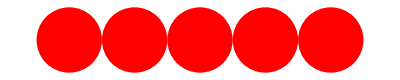

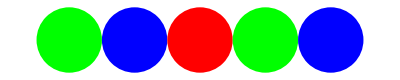
Za dodatni izziv poskusi napisati funkcijo MesaniKrogi[n], ki bo narisala kroge v izmenjajočih barvah. Na primer:
-Graphics-

Na podoben način definiraj še funkcijo NarisiKrogle[n], ki nariše n sfer. Sfere lahko postaviš tudi drugače (ne nujno v ravni vrsti).

Nariši interaktivni 3d graf, ki vsebuje tri zaporedne krogle, vsaki od katerih lahko spreminjaš njeno drugo koordinato.

-Graphics3D-

## Naloga 10

Napiši funkcijo, ki sprejme narvni števili m in n in vrne seznam prvih n členov Collatzovega zaporedja za število m. Pomagaj si s funkcijo “RecurrenceTable”.

```mathematica
Collatz[m_,n_]:=RecurrenceTable[
{
a[k+1]==If[Mod[a[k],2]==0,
Floor[a[k]/2],
3*a[k]+1
],
a[1]==m
},
a,{k,n}
]
```

```mathematica
Collatz[18,5]
```

{18,9,28,14,7}